```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/NANOGrav2PBH"];
```

## Gaussian

### monochromatic

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=ks^(2n-4)Sin[ks r]/(ks r)
```

√As ks^n

(ks^(-5+2 n) Sin[ks r])/r

```mathematica
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

(√3)/ks

### log-normal

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n>0};
```

```mathematica
calPs[k_,ks_,As_,sg_]=As/(√(2π)sg)Exp[(-(Log[k]-Log[ks])^2)/(2 sg^2)];
Simplify[Integrate[calPs[k,ks,As,sg] 1/k,{k,0,∞}]]
```

As

```mathematica
sigman[n_,ks_,As_,sg_]=Simplify[√Integrate[k^(2n)calPs[k,ks,As,sg] 1/k,{k,0,∞}]]
```

√As ⅇ^(n^2 sg^2) ks^n

```mathematica
normN=Simplify[Sum[calPs[E^logk,ks,As,sg],{logk,Log[ks]-sg,Log[ks]+sg,sg}]3sg]/.{As->1}
```

(3 (2+√ⅇ))/(√(2 ⅇ π))

```mathematica
psin[n_,r_,ks_,sg_]=Normal[Series[Simplify[1/(normN sigman[2,ks,As,sg]^2)Sum[Exp[2n logk] Sin[E^logk r]/(E^logk r)calPs[E^logk,ks,As,sg],{logk,Log[ks]-sg,Log[ks]+sg,sg}]3sg],{sg,0,2}]]
```

(ks^(-5+2 n) Sin[ks r])/r-(ks^(-5+2 n) sg^2 (ks r Cos[ks r]-4 ks n r Cos[ks r]+15 Sin[ks r]+8 √ⅇ Sin[ks r]+4 n Sin[ks r]-4 n^2 Sin[ks r]+ks^2 r^2 Sin[ks r]))/((2+√ⅇ) r)

```mathematica
gamma3[sg_]=sigman[3,ks,As,sg]^2/(sigman[2,ks,As,sg]sigman[4,ks,As,sg])
```

ⅇ^(-2 sg^2)

```mathematica
Rb[ks_,sg_]=√3 sigman[3,ks,As,sg]/sigman[4,ks,As,sg]
```

(√3 ⅇ^(-7 sg^2))/ks

```mathematica
zetabar[r_,ks_,mu2_,kb_]=Normal[Series[Simplify[mu2/(1-gamma3[sg]^2)(psin[1,r,ks,sg]-1/3 Rb[ks,sg]^2 psin[2,r,ks,sg])-mu2 kb^2 sigman[2,ks,As,sg]/(sigman[4,ks,As,sg]gamma3[sg](1-gamma3[sg]^2))(gamma3[sg]^2 psin[1,r,ks,sg]-1/3 Rb[ks,sg]^2 psin[2,r,ks,sg])],{sg,0,2}]]/.{sg->0}
```

(mu2 (-4 ks (-kb^2+ks^2) r Cos[ks r]+((-12-10 √ⅇ) kb^2+(20+14 √ⅇ) ks^2) Sin[ks r]))/(4 (2+√ⅇ) ks^5 r)

```mathematica
zetaks[r_,ks_,mu2_]=zetabar[r,ks,mu2,ks]//Simplify
```

(mu2 Sin[ks r])/(ks^3 r)

```mathematica
zetax[x_,mu_]=zetaks[x/ks,ks,mu ks^2]//Simplify
```

(mu Sin[x])/x

```mathematica
CompactC[x_,mu_]=(1-(1+x D[zetax[x,mu], x])^2)/3//Simplify
```

(x^2-(x+mu x Cos[x]-mu Sin[x])^2)/(3 x^2)

```mathematica
rmcond[x_]=-x^2/mu(D[zetax[x,mu], x]+x D[D[zetax[x,mu], x], x])//Simplify
```

x Cos[x]+(-1+x^2) Sin[x]

```mathematica
xm=x/.FindRoot[rmcond[x]==0,{x,3}]
```

2.74371

```mathematica
Simplify[Solve[CompactC[x,mu]==Cth,mu]]/.{x->xm,Cth->0.267}
```

{{mu→0.521027},{mu→1.36026}}

```mathematica
Sin[xm]/xm
```

0.141221

```mathematica
xm/(6.4 10^-14)
```

4.28704×10^13

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

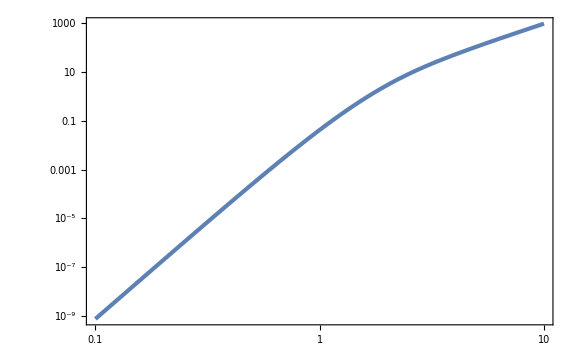

```mathematica
LogLogPlot[f[z],{z,0.1,10}]
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
((1/0.12 1/(2.4 10^4)10^20 gineV(3/(2π))^(3/2)(4.3 10^13 MpcinvineV)^3)/(π^2/30 3.38(2.725KineV)^4 0.28))^-1
```

7.10265×10^-18

```mathematica
((10^20 gineV(3/(2π))^(3/2)(4.3 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2 0.28))^-1
```

7.07168×10^-18

```mathematica
mu2[M_]=Log[M/10^20]/0.28;
```

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
mu2th=0.521;
```

```mathematica
fPBH[M_,As_]=M/10^20(f[mu2[M]/(√As)]PG[mu2[M],As])/(7.1 10^-18)UnitStep[mu2[M]-mu2th];
```

```mathematica
fPBH[1.18 10^20,2.8 10^-3]
```

1.35757×10^-6

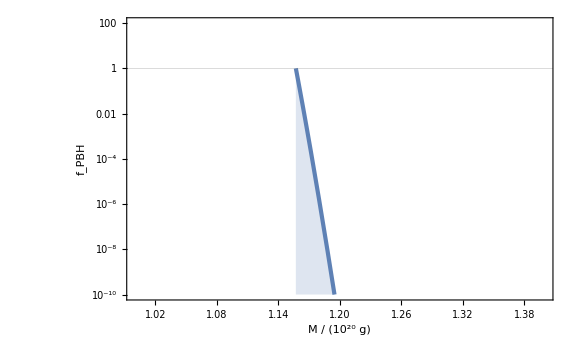

```mathematica
FigfPBH=LogPlot[fPBH[M 10^20,2.8 10^-3],{M,1,1.4},GridLines->{None,{1}},PlotRange->{{1,1.4},{10^-10,100}},Filling->Bottom,FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

### scale-invariant

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0};
```

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
psin[n_,r_,kW_]=1/sigman[2,kW]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

(2 kW^(-4+2 n) HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2])/n

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(4-4 Cos[kW r])/(kW^4 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamma3=sigman[3,kW,As]^2/(sigman[2,kW,As]sigman[4,kW,As])
Rb[kW_]=√3 sigman[3,kW]/sigman[4,kW]
```

(2 √2)/3

2/kW

```mathematica
zetabar[r_,kW_,mu2_,kb_]=mu2/(1-gamma3^2)(psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])-mu2 kb^2 sigman[2,kW,As]/(sigman[4,kW,As]gamma3(1-gamma3^2))(gamma3^2 psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])//Simplify
```

(12 mu2 (-12 kb^2+8 kW^2-4 kb^2 kW^2 r^2+3 kW^4 r^2+(kW^2 (-8+kW^2 r^2)-2 kb^2 (-6+kW^2 r^2)) Cos[kW r]+4 kW (3 kb^2-2 kW^2) r Sin[kW r]))/(kW^8 r^4)

```mathematica
zetax[x_,mu_,kappa_]=zetabar[x/kW,kW,mu kW^2,kappa kW]//Simplify
```

-(12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4

```mathematica
CompactC[x_,mu_,kappa_]=(1-(1+x D[zetax[x,mu,kappa], x])^2)/3//Simplify
```

1/3 (1-1/x^8(-384 mu+576 kappa^2 mu-72 mu x^2+96 kappa^2 mu x^2+x^4+24 mu (16-5 x^2+8 kappa^2 (-3+x^2)) Cos[x]+12 mu x (32-x^2+2 kappa^2 (-24+x^2)) Sin[x])^2)

```mathematica
xmcond[x_,kappa_]=(D[zetax[x,mu,kappa], x]+x D[D[zetax[x,mu,kappa], x], x])x^5/(12mu)//Simplify
```

4 (32+3 x^2-4 kappa^2 (12+x^2))+(-128+52 x^2-x^4+2 kappa^2 (96-40 x^2+x^4)) Cos[x]-x (128-11 x^2+6 kappa^2 (-32+3 x^2)) Sin[x]

```mathematica
FindRoot[xmcond[x,kappa]==0,{x,Min[3/kappa,5]},WorkingPrecision->30]/.{kappa->0.1}
```

FindRoot::srect: Value Min[5.,3./kappa] in search specification {x,Min[3/kappa,5]} is not a number or array of numbers.

FindRoot::precw: The precision of the argument function (4 (32+3 x^2-0.04 (12+x^2))+(-128+52 x^2-x^4+0.02 (96-40 Power[«2»]+x^4)) Cos[x]-x (128-11 x^2+0.06 (-32+3 Power[«2»])) Sin[x]==0) is less than WorkingPrecision (30.).

{x→5.3605653423668734007907946457}

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk]==0,{x,Min[5/10^logk,5]},WorkingPrecision->30]//Quiet},{logk,-3,2,1/100}];
```

```mathematica
Last[xmList][[2]]100
First[xmList][[2]]
```

2.23610391498593770655394732721

5.37014187909902279530303052317

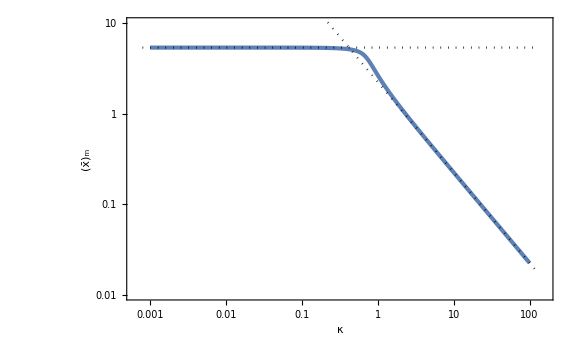

```mathematica
Figxm=Show[ListLogLogPlot[xmList,PlotRange->{{10^-3.2,10^2.2},{0.01,10}},FrameLabel->{κ,Subscript[OverBar[x], "m"]}],LogLogPlot[{2.24/k,5.37},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==0.267,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

```mathematica
Solve[CompactC[5.37,mu,0]==0.267,mu]
```

{{mu→0.102313},{mu→0.26711}}

```mathematica
Normal[Series[mu/.Solve[Collect[Normal[Series[Simplify[CompactC[2.24/kappa,mu,kappa]],{kappa,∞,4}]],mu]==0.267,mu][[1]],{kappa,∞,2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.322681+0.2539/kappa^2+0.664695 kappa^2

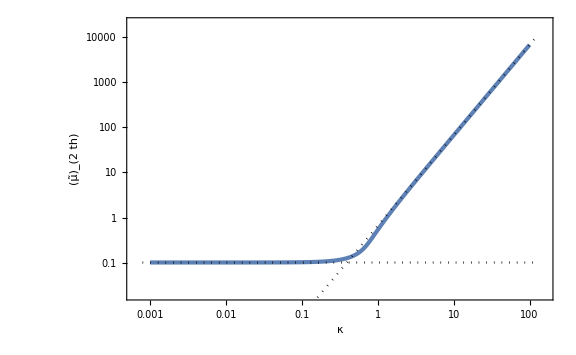

```mathematica
Figmuth=Show[ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]},PlotRange->{{10^-3.2,10^2.2},{0.02,2 10^4}}],LogLogPlot[{0.102,0.665 k^2},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

```mathematica
gm[kappa_]=zetax[xmint[kappa],mu,kappa]/mu//Simplify;
```

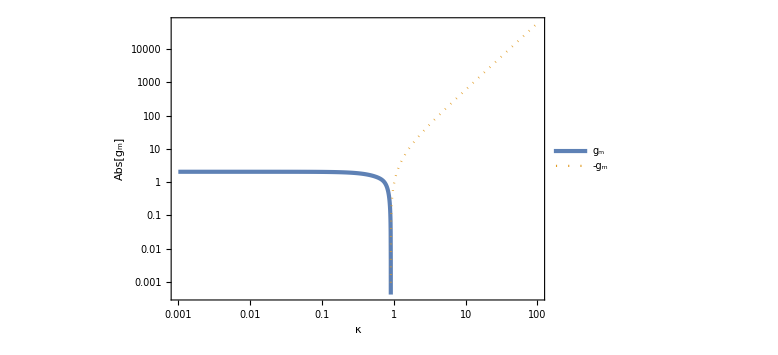

```mathematica
Figgm=LogLogPlot[{gm[kappa],-gm[kappa]},{kappa,10^-3,10^2},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dotted},FrameLabel->{κ,Abs[Subscript[g, "m"]]},PlotLegends->Placed[{Subscript[g, "m"],-Subscript[g, "m"]},{0.2,0.8}]]
```

```mathematica
kappac=kappa/.FindRoot[gm[kappa]==0,{kappa,1}]
```

0.90878

```mathematica
(6.4 10^-14)^-1
```

1.5625×10^13

```mathematica
sigman[4,kW,As]^2/(sigman[2,kW,As] sigman[3,kW,As]^3)
```

(3 √(3/2))/(As kW^3)

```mathematica
sigman[4,kW,As]
```

(√As kW^4)/(2 √2)

```mathematica
sigman[2,kW,As]
```

(√As kW^2)/2

```mathematica
sigman[3,kW]^2/sigman[2,kW,As]^2
```

(2 kW^2)/3

```mathematica
MoMkW[mu_,kappa_]=xmint[kappa]^2 Exp[2mu gm[kappa]];
```

```mathematica
MContour=Table[i,{i,-5,5,1/4}];
```

```mathematica
FigMoMkW=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappac]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{Row[{Subscript["log", 10]," ",κ}],Subscript["log", 10] Subscript[OverTilde[μ], 2]}],ContourPlot[MoMkW[10^logm,10^logk]==MoMkW[muthint[10^-3],10^-3],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
Mc=MoMkW[0.1,kappac]
Mth=MoMkW[muthint[10^-3],10^-3]
```

9.17143

43.762

```mathematica
muthint[10^-3]
```

0.102313

```mathematica
muM[kappa_,MM_]=1/(2gm[kappa])Log[MM/xmint[kappa]^2];
```

```mathematica
FindRoot[muM[kappa,30]==muthint[kappa],{kappa,0.7}]
```

{kappa→0.701322}

```mathematica
FindRoot[muM[kappa,0.001]==muthint[kappa],{kappa,2}]
```

{kappa→1.28126}

```mathematica
kappathList1=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.908}]},{logM,Log10[Mc]+1/1000,Log10[Mth],1/100}];
```

```mathematica
kappathList2=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.91}]},{logM,-3,Log10[Mc],1/100}];
```

```mathematica
kappathList=Join[kappathList2,kappathList1];
```

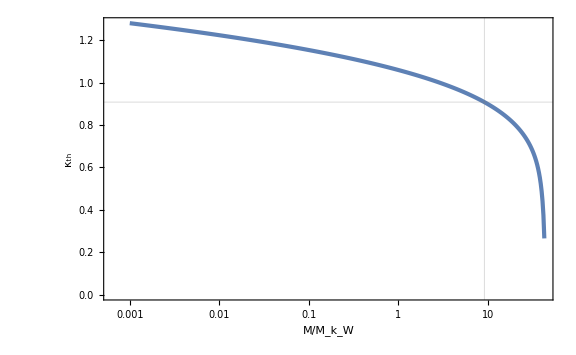

```mathematica
Figkappath=ListLogLinearPlot[kappathList,FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},GridLines->{{Mc},{kappac}}]
```

```mathematica
kappathint[MM_]=Interpolation[kappathList][MM];
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

```mathematica
npk[mu_,kappa_,As_]=1/(2π)^(3/2)27(√3)/8 f[2 √2 mu kappa^2/(√As)]PG[mu,0,As/8]PG[kappa^2,2/3,As/(24 mu^2)]kappa;
```

```mathematica
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappac,kappathint[MM]}]/;MM<Mc
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappathint[MM],kappac}]/;Mc<MM<Mth
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,0,kappac}]/;MM>Mth
```

```mathematica
nPBH[10,0.0028]
```

3.90138×10^-116

```mathematica
nPBHList1=ParallelTable[{10^logM,nPBH[10^logM,0.01]},{logM,1,2,1/100}];//AbsoluteTiming
nPBHList2=ParallelTable[{10^logM,nPBH[10^logM,0.0028]},{logM,1,2,1/100}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{73.3518,Null}

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{110.149,Null}

```mathematica
Export["nPBH1e-2.dat",nPBHList1];
Export["nPBH28e-4.dat",nPBHList2];
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHList1=Map[Log10,nPBHList1,{2}]//Simplify;
LognPBHList2=Map[Log10,nPBHList2,{2}]//Simplify;
```

```mathematica
nPBHint1[MM_]=10^(Interpolation[LognPBHList1][Log10[MM]]);
nPBHint2[MM_]=10^(Interpolation[LognPBHList2][Log10[MM]]);
```

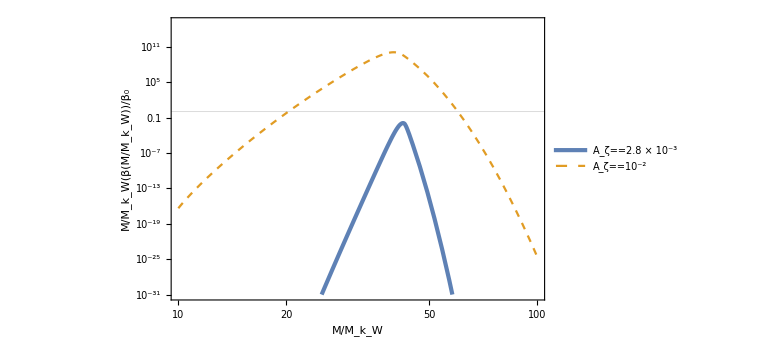

```mathematica
FigBeta=LogLogPlot[{MM nPBHint2[MM]/n2f,MM nPBHint1[MM]/n2f},{MM,10,100},PlotRange->{10^-31,10^15},GridLines->{None,{1}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Row[{M/Subscript[M, Subscript[k, "W"]],β[Row[{M,"/",Subscript[M, Subscript[k, "W"]]}]]/Subscript[β, 0]}]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}],Subscript[A, ζ]==Superscript[10,-2]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.25,0.2}]]
```

```mathematica
MaxfPBH=FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[1]]
MaxMM=MM/.FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[2]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0115842

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

42.2278

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2797.23 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2376.04 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2002.41 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

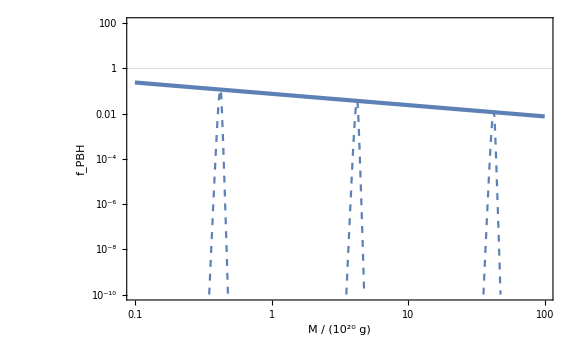

```mathematica
FigfPBH=LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2)},{MM,0.1,100},PlotRange->{10^-10,100},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]}},FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

## non-Gaussian

### monochromatic

```mathematica
sigman[n_,ks_,As_]=ks^n √As
psin[n_,r_,ks_]=ks^(2n-4)Sin[ks r]/(ks r)
```

√As ks^n

(ks^(-5+2 n) Sin[ks r])/r

```mathematica
gamma1=sigman[1,ks,As]^2/(sigman[0,ks,As]sigman[2,ks,As])
gamma2=sigman[2,ks,As]^2/(sigman[0,ks,As]sigman[4,ks,As])
gamma3=sigman[3,ks,As]^2/(sigman[2,ks,As]sigman[4,ks,As])
Rb[ks_]=√3 sigman[3,ks,As]/sigman[4,ks,As]
```

1

1

1

(√3)/ks

```mathematica
zetaGx[x_,mu_]=mu Sin[x]/x//Simplify
```

(mu Sin[x])/x

```mathematica
zetabar[x_,mu_,fNL_]=zetaGx[x,mu]+3/5 fNL zetaGx[x,mu]^2//Simplify
```

(mu Sin[x] (5 x+3 fNL mu Sin[x]))/(5 x^2)

```mathematica
CompactC[x_,mu_,fNL_]=1/3(1-(1+x D[zetabar[x,mu,fNL], x])^2)//Simplify
```

1/3 (1-((5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x]))^2)/(25 x^4))

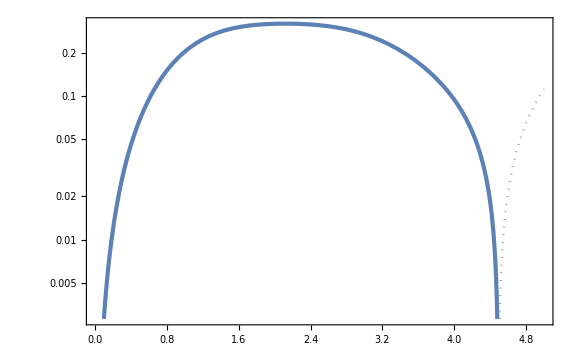

```mathematica
LogPlot[{CompactC[x,0.5,3],-CompactC[x,0.5,3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

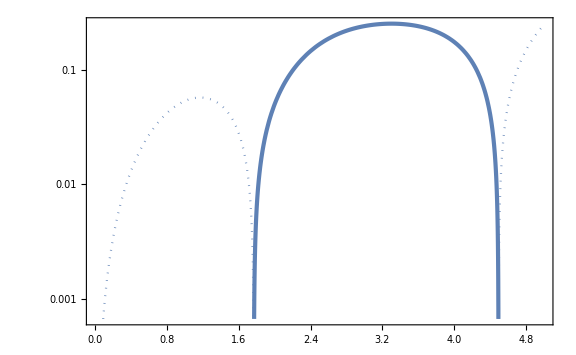

```mathematica
LogPlot[{CompactC[x,0.5,-3],-CompactC[x,0.5,-3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}}]
```

```mathematica
rmcond[x_,mu_,fNL_]=(5 x^3)/mu(D[zetabar[x,mu,fNL], x]+x D[D[zetabar[x,mu,fNL], x], x])//Simplify
```

6 fNL mu-5 x^2 Cos[x]+6 fNL mu (-1+x^2) Cos[2 x]+5 x Sin[x]-5 x^3 Sin[x]-9 fNL mu x Sin[2 x]

```mathematica
rmcond2[x_,mu_,fNL_]=5 x^2(1+x D[zetabar[x,mu,fNL], x])//Simplify
```

5 x^2-5 mu x Sin[x]-6 fNL mu^2 Sin[x]^2+mu x Cos[x] (5 x+6 fNL mu Sin[x])

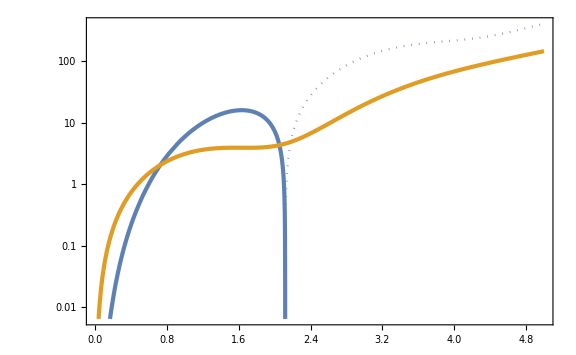

```mathematica
LogPlot[{-rmcond[x,0.5,3],rmcond[x,0.5,3],rmcond2[x,0.5,3],-rmcond2[x,0.5,3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

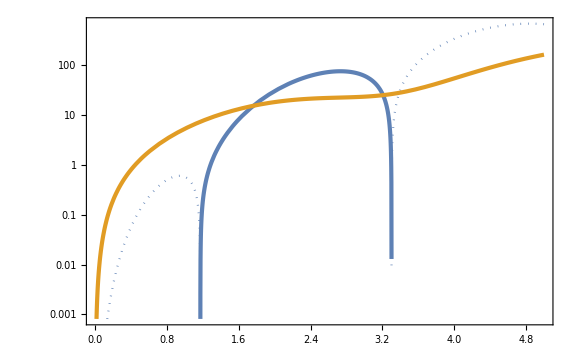

```mathematica
LogPlot[{-rmcond[x,0.5,-3],rmcond[x,0.5,-3],rmcond2[x,0.5,-3],-rmcond2[x,0.5,-3]},{x,0,5},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{AbsoluteThickness[3],Color[2]},{Color[2],Dotted}}]
```

```mathematica
FindRoot[rmcond[x,0.5,3]==0,{x,3}]
```

{x→2.1157}

```mathematica
xmList=Table[{mufNL,x/.FindRoot[rmcond[x,1,mufNL]==0,{x,3}]},{mufNL,-5/3,5/3,1/10}];
```

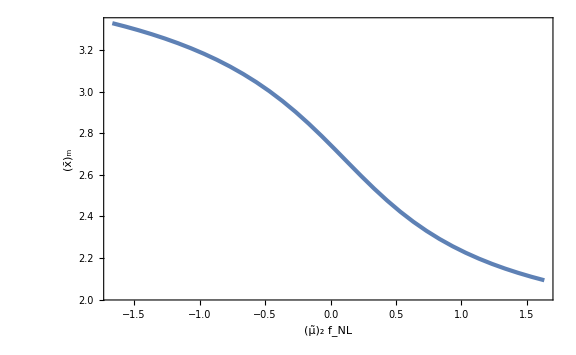

```mathematica
ListPlot[xmList,FrameLabel->{Subscript[OverTilde[μ], 2] Subscript[f, NL],Subscript[OverBar[x], "m"]}]
```

```mathematica
xmint[mufNL_]=Interpolation[xmList][mufNL];
```

```mathematica
Solve[CompactC[xmint[-5/3],mu,1/mu(-5/3)]==0.267,mu]
```

{{mu→0.537651},{mu→1.40366}}

```mathematica
muthList=Table[musol=mu/.Solve[CompactC[xmint[mufNL],mu,mufNL/mu]==0.267,mu][[1]];
{mufNL/musol,musol},{mufNL,-5/3,5/3,1/10}];
```

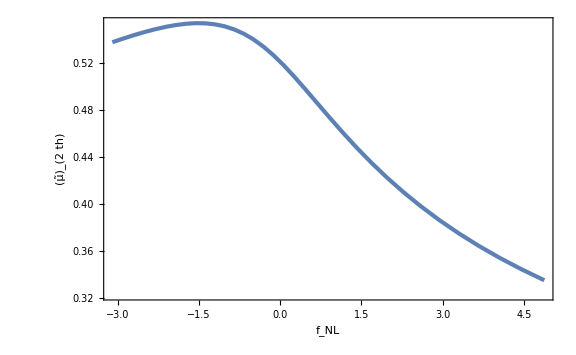

```mathematica
ListPlot[muthList,FrameLabel->{Subscript[f, NL],Subscript[OverTilde[μ], 2th]}]
```

```mathematica
fNLmin=First[muthList][[1]]
fNLmax=Last[muthList][[1]]
```

-3.0999

4.87679

```mathematica
muthint[fNL_]=Interpolation[muthList][fNL];
```

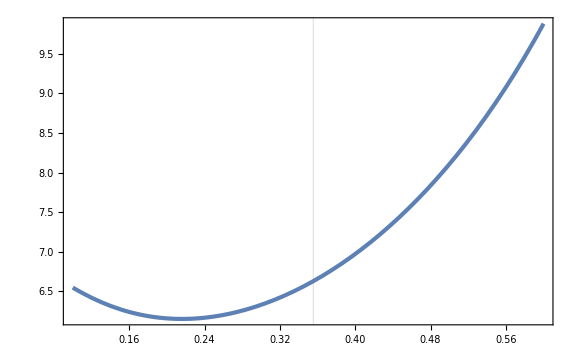

```mathematica
Plot[xmint[mu 4]^2 Exp[2zetabar[xmint[mu 4],mu,4]],{mu,0.1,0.6},GridLines->{{muthint[4]},None}]
```

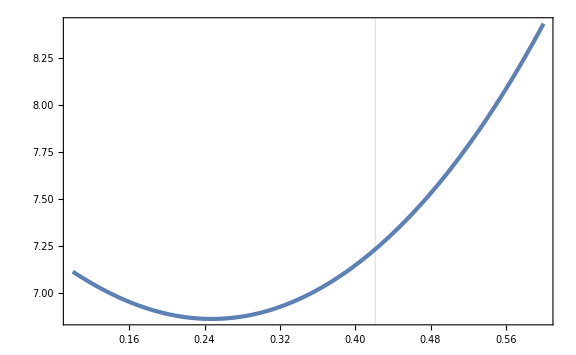

```mathematica
Plot[xmint[mu 2]^2 Exp[2zetabar[xmint[mu 2],mu,2]],{mu,0.1,0.6},GridLines->{{muthint[2]},None}]
```

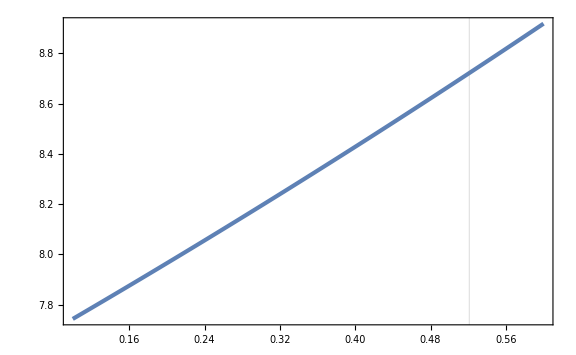

```mathematica
Plot[xmint[mu 0]^2 Exp[2zetabar[xmint[mu 0],mu,0]],{mu,0.1,0.6},GridLines->{{muthint[0]},None}]
```

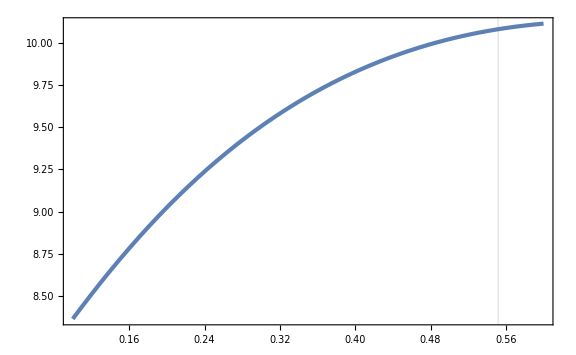

```mathematica
Plot[xmint[mu (-2)]^2 Exp[2zetabar[xmint[mu (-2)],mu,-2]],{mu,0.1,0.6},GridLines->{{muthint[-2]},None}]
```

```mathematica
dLogMdmu[mu_,fNL_]=D[Log[xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]]], mu];
```

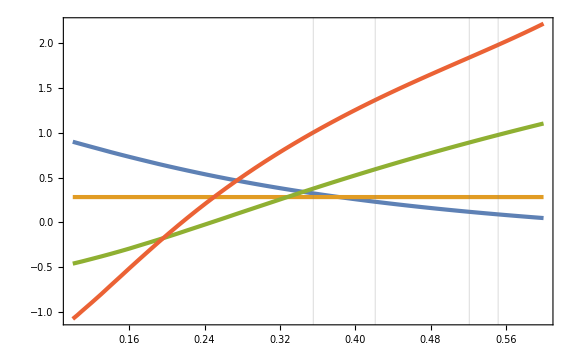

```mathematica
Plot[{dLogMdmu[mu,-2],dLogMdmu[mu,0],dLogMdmu[mu,2],dLogMdmu[mu,4]},{mu,0.1,0.6},GridLines->{{muthint[-2],muthint[0],muthint[2],muthint[4]},None}]
```

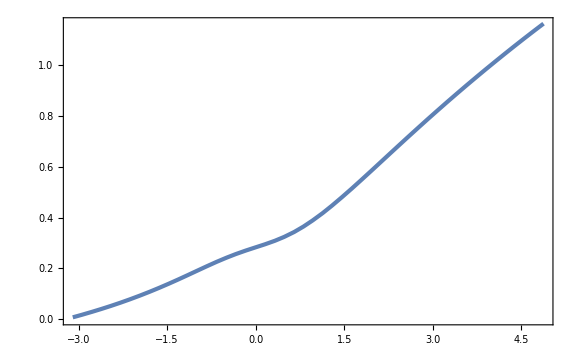

```mathematica
Plot[dLogMdmu[muthint[fNL],fNL],{fNL,fNLmin,fNLmax}(*,FrameLabel->{Subscript[f, NL],Subscript[Abs[Row[{"d log ",M}]/("d"Subscript[OverTilde[μ], 2])], Subscript[OverTilde[μ], 2]==Subscript[OverTilde[μ], 2th]]}*)]
```

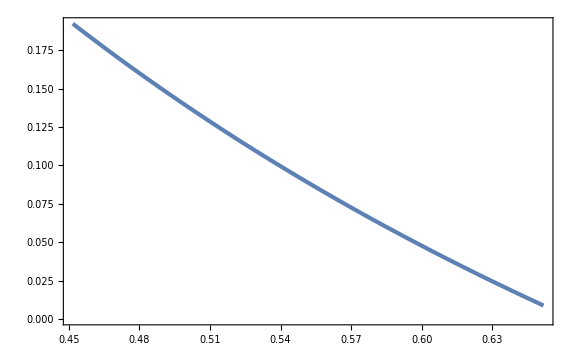

```mathematica
Plot[dLogMdmu[mu,-2],{mu,muthint[-2]-0.1,muthint[-2]+0.1}]
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
((10^20 gineV(3/(2π))^(3/2)(1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100 kminvsinvMpcineV)^2))^-1
```

5.28928×10^-16

```mathematica
PG[x_,sg2_]=1/(√(2π sg2))Exp[-x^2/(2sg2)];
```

```mathematica
MoMks[mu_,fNL_]=xmint[mu fNL]^2 Exp[2zetabar[xmint[mu fNL],mu,fNL]];
```

```mathematica
fPBH[Mks_,ks_,As_,mu_,fNL_]=Mks/10^20 MoMks[mu,fNL](ks/(1.56 10^13))^3(f[mu/(√As)]PG[mu,As])/(5.3 10^-16)dLogMdmu[mu,fNL]^-1 UnitStep[mu-muthint[fNL]];
```

```mathematica
muthint[-2]
```

0.551735

```mathematica
fPBH[10^20,1.56 10^13,2.8 10^-3,0.6,0]
```

7.70761×10^-8

```mathematica
fPBHListfNLm2=Table[{MoMks[mu,-2],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,-2]},{mu,muthint[-2]-0.1,5/3 1/2,0.01}];
fPBHListfNL0=Table[{MoMks[mu,0],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,0]},{mu,muthint[0]-0.1,1,0.01}];
fPBHListfNLp2=Table[{MoMks[mu,2],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,2]},{mu,muthint[2]-0.1,5/3 1/2,0.01}];
fPBHListfNLp4=Table[{MoMks[mu,4],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,4]},{mu,muthint[4]-0.1,5/3 1/4,0.01}];
fPBHListfNLp4Ex=Table[{MoMks[mu,4],fPBH[10^20,1.56 10^13,2.8 10^-3,mu,4]},{mu,5/3 1/4,5/3 1/4+0.05,0.01}];
```

General::munfl: Exp[-708.863] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.864] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-741.043] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.64233} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.66141} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.66667} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

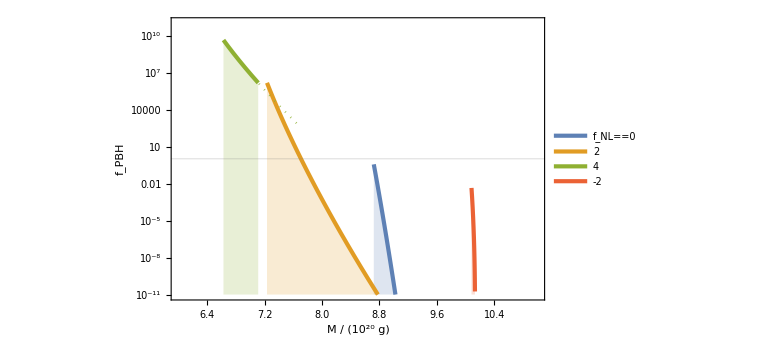

```mathematica
Show[ListLogPlot[{fPBHListfNL0,fPBHListfNLp2,fPBHListfNLp4,fPBHListfNLm2},PlotRange->{{6,11},{10^-11,10^11}},Filling->Bottom,GridLines->{None,{1}},FrameLabel->{Row[{M," / (10^20 g)"}],Subscript[f, PBH]},PlotLegends->Placed[LineLegend[{Subscript[f, NL]==0,2,4,-2},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.8,0.75}]],ListLogPlot[fPBHListfNLp4Ex,PlotStyle->{Color[3],Dotted}]]
```

### scale-invariant

```mathematica
Quit[]
```

```mathematica
$Assumptions={sg>0,ks>0,n>0,As>0,kW>0,kL>0};
```

```mathematica
sigman[n_,kW_,As_]=√(As Integrate[Exp[2n logk],{logk,-∞,Log[kW]}])//Simplify
```

(kW^n √(As/n))/(√2)

```mathematica
sigma0[kW_,As_,kL_]=√(As Integrate[1,{logk,Log[kL],Log[kW]}])//Simplify
```

√(As Log[kW/kL])

```mathematica
psin[n_,r_,kW_]=1/sigman[2,kW,As]^2 As Integrate[k^(2n)Sin[k r]/(k r)1/k,{k,0,kW}]
```

(2 kW^(-4+2 n) HypergeometricPFQ[{n},{3/2,1+n},-1/4 kW^2 r^2])/n

```mathematica
psin[1,r,kW]//Simplify
psin[2,r,kW]//Simplify
```

(4-4 Cos[kW r])/(kW^4 r^2)

(-8+(8-4 kW^2 r^2) Cos[kW r]+8 kW r Sin[kW r])/(kW^4 r^4)

```mathematica
gamma1[kW_,kL_]=sigman[1,kW,As]^2/(sigma0[kW,As,kL]sigman[2,kW,As])//Simplify
gamma2[kW_,kL_]=sigman[2,kW,As]^2/(sigma0[kW,As,kL]sigman[4,kW,As])//Simplify
gamma3=sigman[3,kW,As]^2/(sigman[2,kW,As]sigman[4,kW,As])
Rb[kW_]=√3 sigman[3,kW,As]/sigman[4,kW,As]
```

1/(√Log[kW/kL])

1/(√2 √Log[kW/kL])

(2 √2)/3

2/kW

```mathematica
DD[kW_,kL_]=1-gamma1[kW,kL]^2-gamma2[kW,kL]^2-gamma3^2+2gamma1[kW,kL] gamma2[kW,kL] gamma3
```

1/9-1/(6 Log[kW/kL])

```mathematica
zetaGbar[r_,kW_,mu2_,kb_]=mu2/(1-gamma3^2)(psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])-mu2 kb^2 sigman[2,kW,As]/(sigman[4,kW,As]gamma3(1-gamma3^2))(gamma3^2 psin[1,r,kW]-1/3 Rb[kW]^2 psin[2,r,kW])//Simplify
```

(12 mu2 (-12 kb^2+8 kW^2-4 kb^2 kW^2 r^2+3 kW^4 r^2+(kW^2 (-8+kW^2 r^2)-2 kb^2 (-6+kW^2 r^2)) Cos[kW r]+4 kW (3 kb^2-2 kW^2) r Sin[kW r]))/(kW^8 r^4)

```mathematica
zetaGx[x_,mu_,kappa_]=zetaGbar[x/kW,kW,mu kW^2,kappa kW]//Simplify
```

-(12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4

```mathematica
gx[x_,kappa_]=zetaGx[x,mu,kappa]/mu//Simplify
```

-(12 (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))/x^4

```mathematica
g0[mu_,kappa_]=Limit[gx[x,kappa],{x->0}]
```

6-6 kappa^2

```mathematica
Manipulate[LogLinearPlot[gx[x,10^logk],{x,10^-2,10^2},PlotRange->Full],{logk,-0.1,0.1}]
```

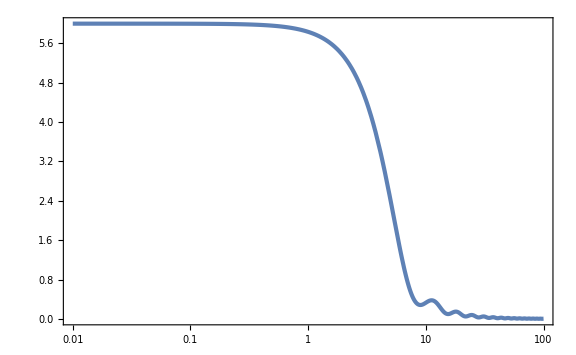

```mathematica
LogLinearPlot[gx[x,0],{x,10^-2,10^2}]
```

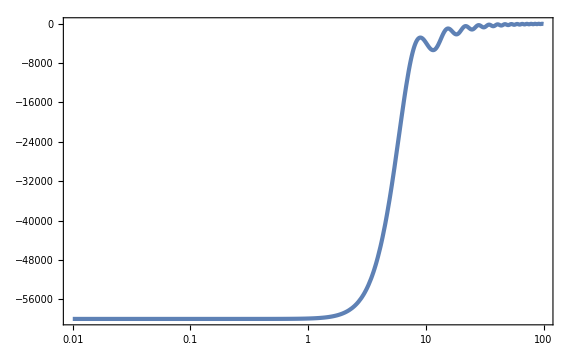

```mathematica
LogLinearPlot[gx[x,10^2],{x,10^-2,10^2}]
```

```mathematica
FindMaximum[{-gx[x,10^(-10^-2)],10^-2<x<6},{x,1}]
```

{0.944161,{x→4.33353}}

```mathematica
Max[FindMaxValue[{gx[x,10^-0.01],10^-2<x<6},{x,1}],FindMaxValue[{-gx[x,10^-0.01],10^-2<x<6},{x,1}]]
```

0.944161

```mathematica
gxMaxList=Table[{10^logk,Max[FindMaxValue[{gx[x,10^logk],10^-2<x<6},{x,1}],FindMaxValue[{-gx[x,10^logk],10^-2<x<6},{x,1}]]},{logk,-1,1,10^-2}];//AbsoluteTiming
```

{173.631,Null}

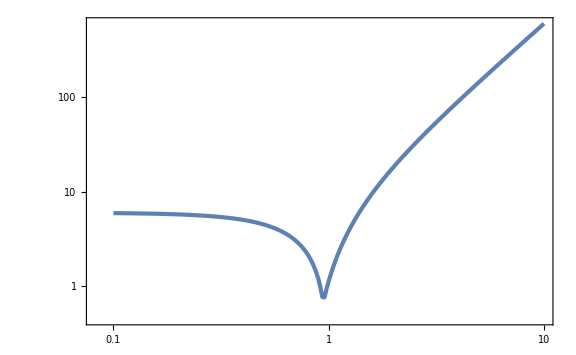

```mathematica
ListLogLogPlot[gxMaxList]
```

```mathematica
gxMaxInt[kappa_]=Interpolation[gxMaxList][kappa];
```

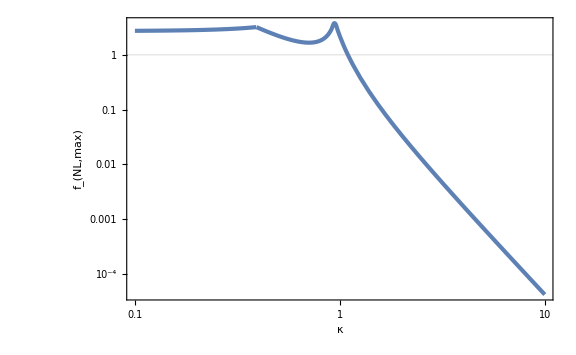

```mathematica
LogLogPlot[(3/5 Max[0.102,0.665 kappa^2]gxMaxInt[kappa])^-1,{kappa,0.1,10},FrameLabel->{κ,Subscript[f, NL,max]},GridLines->{None,{1}}]
```

```mathematica
zetabar[x_,mu_,kappa_,zetainf_,fNL_]=(1+6/5 fNL zetainf)zetaGx[x,mu,kappa]+3/5 fNL zetaGx[x,mu,kappa]^2//Simplify
```

1/(5 x^8)12 mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]) (-x^4 (5+6 fNL zetainf)+36 fNL mu (-8+12 kappa^2-3 x^2+4 kappa^2 x^2+(8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-4 (-2+3 kappa^2) x Sin[x]))

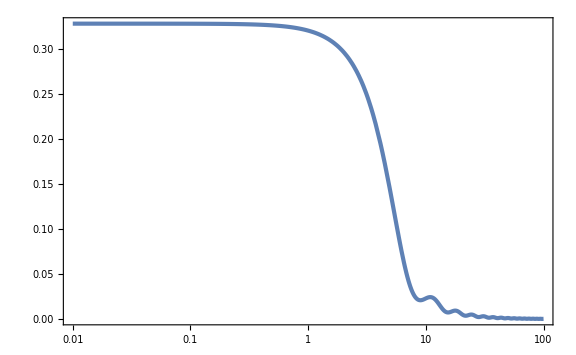

```mathematica
LogLinearPlot[zetabar[x,0.1,0.5,0,-1],{x,0.01,100},PlotRange->Full]
```

```mathematica
CompactC[x_,mu_,kappa_,zetainf_,fNL_]=(1-(1+x D[zetabar[x,mu,kappa,zetainf,fNL], x])^2)/3//Simplify
```

1/3 (1-(1-1/(5 x^8)24 mu (x Cos[x/2]-2 Sin[x/2]) (4 (-2+3 kappa^2) x Cos[x/2]+(16-x^2+2 kappa^2 (-12+x^2)) Sin[x/2]) (-576 fNL mu+864 fNL kappa^2 mu-216 fNL mu x^2+288 fNL kappa^2 mu x^2-5 x^4-6 fNL x^4 zetainf+72 fNL mu (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-288 fNL (-2+3 kappa^2) mu x Sin[x]))^2)

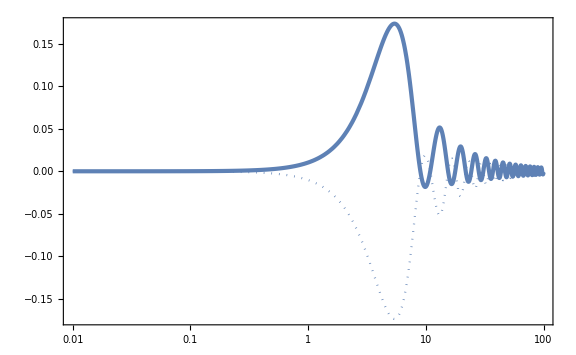

```mathematica
LogLinearPlot[{CompactC[x,0.1,0.5,0,-1],-CompactC[x,0.1,0.5,0,-1]},{x,0.01,100},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted}},PlotRange->Full]
```

```mathematica
xmcond[x_,mu_,kappa_,zetainf_,fNL_]=(5 x^9)/(12mu)(D[zetabar[x,mu,kappa,zetainf,fNL], x]+x D[D[zetabar[x,mu,kappa,zetainf,fNL], x], x])//Simplify
```

221184 fNL mu-663552 fNL kappa^2 mu+497664 fNL kappa^4 mu+93312 fNL mu x^2-264384 fNL kappa^2 mu x^2+186624 fNL kappa^4 mu x^2+640 x^4-960 kappa^2 x^4+5472 fNL mu x^4-14976 fNL kappa^2 mu x^4+10368 fNL kappa^4 mu x^4+60 x^6-80 kappa^2 x^6+768 fNL x^4 zetainf-1152 fNL kappa^2 x^4 zetainf+72 fNL x^6 zetainf-96 fNL kappa^2 x^6 zetainf+(5 x^4 (-128+52 x^2-x^4+2 kappa^2 (96-40 x^2+x^4))-6 fNL (12 mu (4096-320 x^2-280 x^4+3 x^6+8 kappa^4 (1152-144 x^2-73 x^4+x^6)-2 kappa^2 (6144-624 x^2-406 x^4+5 x^6))+x^4 (128-52 x^2+x^4-2 kappa^2 (96-40 x^2+x^4)) zetainf)) Cos[x]-72 fNL mu (-1024+1616 x^2-156 x^4+x^6-4 kappa^2 (-768+1230 x^2-129 x^4+x^6)+4 kappa^4 (-576+936 x^2-106 x^4+x^6)) Cos[2 x]-294912 fNL mu x Sin[x]+884736 fNL kappa^2 mu x Sin[x]-663552 fNL kappa^4 mu x Sin[x]-51264 fNL mu x^3 Sin[x]+140256 fNL kappa^2 mu x^3 Sin[x]-95040 fNL kappa^4 mu x^3 Sin[x]-640 x^5 Sin[x]+960 kappa^2 x^5 Sin[x]+3240 fNL mu x^5 Sin[x]-9936 fNL kappa^2 mu x^5 Sin[x]+7488 fNL kappa^4 mu x^5 Sin[x]+55 x^7 Sin[x]-90 kappa^2 x^7 Sin[x]-768 fNL x^5 zetainf Sin[x]+1152 fNL kappa^2 x^5 zetainf Sin[x]+66 fNL x^7 zetainf Sin[x]-108 fNL kappa^2 x^7 zetainf Sin[x]+147456 fNL mu x Sin[2 x]-442368 fNL kappa^2 mu x Sin[2 x]+331776 fNL kappa^4 mu x Sin[2 x]-48096 fNL mu x^3 Sin[2 x]+151056 fNL kappa^2 mu x^3 Sin[2 x]-118368 fNL kappa^4 mu x^3 Sin[2 x]+1404 fNL mu x^5 Sin[2 x]-5040 fNL kappa^2 mu x^5 Sin[2 x]+4464 fNL kappa^4 mu x^5 Sin[2 x]

```mathematica
xmcond2[x_,mu_,kappa_,zetainf_,fNL_]=(1+x D[zetabar[x,mu,kappa,zetainf,fNL], x])//Simplify
```

1-1/(5 x^8)24 mu (x Cos[x/2]-2 Sin[x/2]) (4 (-2+3 kappa^2) x Cos[x/2]+(16-x^2+2 kappa^2 (-12+x^2)) Sin[x/2]) (-576 fNL mu+864 fNL kappa^2 mu-216 fNL mu x^2+288 fNL kappa^2 mu x^2-5 x^4-6 fNL x^4 zetainf+72 fNL mu (8-x^2+2 kappa^2 (-6+x^2)) Cos[x]-288 fNL (-2+3 kappa^2) mu x Sin[x])

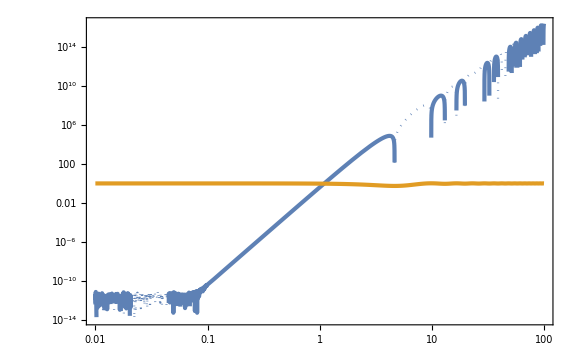

```mathematica
LogLogPlot[{-xmcond[x,0.1,0.5,0,1],xmcond[x,0.1,0.5,0,1],xmcond2[x,0.1,0.5,0,1],-xmcond2[x,0.1,0.5,0,1]},{x,0.01,100},PlotStyle->{AbsoluteThickness[3],{Color[1],Dotted},{Color[2],AbsoluteThickness[3]},{Color[2],Dotted}}]
```

```mathematica
FindRoot[xmcond[x,kappa]==0,{x,Min[3/kappa,5]},WorkingPrecision->30]/.{kappa->0.1}
```

FindRoot::srect: Value Min[5.,3./kappa] in search specification {x,Min[3/kappa,5]} is not a number or array of numbers.

FindRoot::precw: The precision of the argument function (4 (32+3 x^2-0.04 (12+x^2))+(-128+52 x^2-x^4+0.02 (96-40 Power[«2»]+x^4)) Cos[x]-x (128-11 x^2+0.06 (-32+3 Power[«2»])) Sin[x]==0) is less than WorkingPrecision (30.).

{x→5.3605653423668734007907946457}

```mathematica
xmList=Table[{10^logk,x/.FindRoot[xmcond[x,10^logk]==0,{x,Min[5/10^logk,5]},WorkingPrecision->30]//Quiet},{logk,-3,2,1/100}];
```

```mathematica
Last[xmList][[2]]100
First[xmList][[2]]
```

2.23610391498593770655394732721

5.37014187909902279530303052317

```mathematica
Figxm=Show[ListLogLogPlot[xmList,PlotRange->{{10^-3.2,10^2.2},{0.01,10}},FrameLabel->{κ,Subscript[OverBar[x], "m"]}],LogLogPlot[{2.24/k,5.37},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

-Graphics-

```mathematica
xmint[kappa_]=Interpolation[xmList][kappa];
```

```mathematica
Cmax[mu_,kappa_]=CompactC[xmint[kappa],mu,kappa];
```

```mathematica
muthList=Table[{10^logk,mu/.Solve[Cmax[mu,10^logk]==0.267,mu][[1]]},{logk,-3,2,1/100}];
```

```mathematica
muthint[kappa_]=Interpolation[muthList][kappa];
```

```mathematica
Solve[CompactC[5.37,mu,0]==0.267,mu]
```

{{mu→0.102313},{mu→0.26711}}

```mathematica
Normal[Series[mu/.Solve[Collect[Normal[Series[Simplify[CompactC[2.24/kappa,mu,kappa]],{kappa,∞,4}]],mu]==0.267,mu][[1]],{kappa,∞,2}]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.322681+0.2539/kappa^2+0.664695 kappa^2

```mathematica
Figmuth=Show[ListLogLogPlot[muthList,FrameLabel->{κ,Subscript[OverTilde[μ], 2th]},PlotRange->{{10^-3.2,10^2.2},{0.02,2 10^4}}],LogLogPlot[{0.102,0.665 k^2},{k,10^-3.1,10^2.1},PlotStyle->{{Black,Dotted}}]]
```

-Graphics-

```mathematica
gm[kappa_]=zetax[xmint[kappa],mu,kappa]/mu//Simplify;
```

```mathematica
Figgm=LogLogPlot[{gm[kappa],-gm[kappa]},{kappa,10^-3,10^2},PlotRange->Full,PlotStyle->{AbsoluteThickness[3],Dotted},FrameLabel->{κ,Abs[Subscript[g, "m"]]},PlotLegends->Placed[{Subscript[g, "m"],-Subscript[g, "m"]},{0.2,0.8}]]
```

-Graphics-

```mathematica
kappac=kappa/.FindRoot[gm[kappa]==0,{kappa,1}]
```

0.90878

```mathematica
(6.4 10^-14)^-1
```

1.5625×10^13

```mathematica
sigman[4,kW,As]^2/(sigman[2,kW,As] sigman[3,kW,As]^3)
```

(3 √(3/2))/(As kW^3)

```mathematica
sigman[4,kW,As]
```

(√As kW^4)/(2 √2)

```mathematica
sigman[2,kW,As]
```

(√As kW^2)/2

```mathematica
sigman[3,kW]^2/sigman[2,kW,As]^2
```

(2 kW^2)/3

```mathematica
MoMkW[mu_,kappa_]=xmint[kappa]^2 Exp[2mu gm[kappa]];
```

```mathematica
MContour=Table[i,{i,-5,5,1/4}];
```

```mathematica
FigMoMkW=Show[ContourPlot[Log10[MoMkW[10^logm,10^logk]],{logk,-3,0.5},{logm,-2,0.5},Contours->MContour,PlotLegends->BarLegend[Automatic,LegendLabel->Row[{Subscript["log", 10],M[Subscript[OverTilde[μ], 2],κ]/Subscript[M, Subscript[k, "W"]]}]],GridLines->{{Log10[kappac]},None},GridLinesStyle->Directive[Black,Dotted,AbsoluteThickness[2]],FrameLabel->{Row[{Subscript["log", 10]," ",κ}],Subscript["log", 10] Subscript[OverTilde[μ], 2]}],ContourPlot[MoMkW[10^logm,10^logk]==MoMkW[muthint[10^-3],10^-3],{logk,-3,0.5},{logm,-2,0.5},ContourStyle->{Black,AbsoluteThickness[2]}],Plot[Log10[muthint[10^logk]],{logk,-3,2},PlotStyle->{AbsoluteThickness[3],Color[4]}]]
```

-Graphics-

```mathematica
Mc=MoMkW[0.1,kappac]
Mth=MoMkW[muthint[10^-3],10^-3]
```

9.17143

43.762

```mathematica
muthint[10^-3]
```

0.102313

```mathematica
muM[kappa_,MM_]=1/(2gm[kappa])Log[MM/xmint[kappa]^2];
```

```mathematica
FindRoot[muM[kappa,30]==muthint[kappa],{kappa,0.7}]
```

{kappa→0.701322}

```mathematica
FindRoot[muM[kappa,0.001]==muthint[kappa],{kappa,2}]
```

{kappa→1.28126}

```mathematica
kappathList1=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.908}]},{logM,Log10[Mc]+1/1000,Log10[Mth],1/100}];
```

```mathematica
kappathList2=Table[{10^logM,kappa/.FindRoot[muM[kappa,10^logM]==muthint[kappa],{kappa,0.91}]},{logM,-3,Log10[Mc],1/100}];
```

```mathematica
kappathList=Join[kappathList2,kappathList1];
```

```mathematica
Figkappath=ListLogLinearPlot[kappathList,FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Subscript[κ, th]},GridLines->{{Mc},{kappac}}]
```

-Graphics-

```mathematica
kappathint[MM_]=Interpolation[kappathList][MM];
```

```mathematica
f[z_]=1/2 z(z^2-3)(Erf[1/2 √(5/2)z]+Erf[√(5/2)z])+√(2/(5π))((8/5+31/4 z^2)Exp[-5/8 z^2]+(-8/5+1/2 z^2)Exp[-5/2 z^2]);
PG[z_,m_,s2_]=1/(√(2π s2))Exp[(-(z-m)^2)/(2s2)];
```

```mathematica
npk[mu_,kappa_,As_]=1/(2π)^(3/2)27(√3)/8 f[2 √2 mu kappa^2/(√As)]PG[mu,0,As/8]PG[kappa^2,2/3,As/(24 mu^2)]kappa;
```

```mathematica
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappac,kappathint[MM]}]/;MM<Mc
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,kappathint[MM],kappac}]/;Mc<MM<Mth
nPBH[MM_,As_]:=NIntegrate[2gm[kappa]npk[muM[kappa,MM],kappa,As],{kappa,0,kappac}]/;MM>Mth
```

```mathematica
nPBH[10,0.0028]
```

3.90138×10^-116

```mathematica
nPBHList1=ParallelTable[{10^logM,nPBH[10^logM,0.01]},{logM,1,2,1/100}];//AbsoluteTiming
nPBHList2=ParallelTable[{10^logM,nPBH[10^logM,0.0028]},{logM,1,2,1/100}];//AbsoluteTiming
```

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{73.3518,Null}

InterpolatingFunction::dmval: 
                     16/25
   Input value {10 10     } lies outside the range of data in the
     interpolating function. Extrapolation will be used.

{110.149,Null}

```mathematica
Export["nPBH1e-2.dat",nPBHList1];
Export["nPBH28e-4.dat",nPBHList2];
```

```mathematica
gineV=(1.783 10^-33)^-1;
MpcinvineV=(10^6 3.086 10^16)^-1 1.973 10^-7;
KineV=(1.16 10^4)^-1;
MplineV=2.435 10^(18+9);
kminvsinvMpcineV=(10^3 6.582 10^-16)/(3.086 10^16 10^6);
```

```mathematica
n2f=((10^20 gineV (1.56 10^13 MpcinvineV)^3)/(0.12 3 MplineV^2(100kminvsinvMpcineV)^2))^-1
```

1.74505×10^-16

```mathematica
LognPBHList1=Map[Log10,nPBHList1,{2}]//Simplify;
LognPBHList2=Map[Log10,nPBHList2,{2}]//Simplify;
```

```mathematica
nPBHint1[MM_]=10^(Interpolation[LognPBHList1][Log10[MM]]);
nPBHint2[MM_]=10^(Interpolation[LognPBHList2][Log10[MM]]);
```

```mathematica
FigBeta=LogLogPlot[{MM nPBHint2[MM]/n2f,MM nPBHint1[MM]/n2f},{MM,10,100},PlotRange->{10^-31,10^15},GridLines->{None,{1}},FrameLabel->{Row[{M,"/",Subscript[M, Subscript[k, "W"]]}],Row[{M/Subscript[M, Subscript[k, "W"]],β[Row[{M,"/",Subscript[M, Subscript[k, "W"]]}]]/Subscript[β, 0]}]},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->Placed[LineLegend[{Row[{Subscript[A, ζ]==2.8," × ",Superscript[10,-3]}],Subscript[A, ζ]==Superscript[10,-2]},LabelStyle->Directive[Larger,Black,FontFamily->"Palatino"]],{0.25,0.2}]]
```

-Graphics-

```mathematica
MaxfPBH=FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[1]]
MaxMM=MM/.FindMaximum[MM nPBHint2[MM]/n2f,{MM,40}][[2]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.0115842

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

42.2278

```mathematica
FigfPBH=LogLogPlot[{0.01^-0.5 MM/0.01 nPBHint2[MM/0.01]/n2f,0.1^-0.5 MM/0.1 nPBHint2[MM/0.1]/n2f,MM nPBHint2[MM]/n2f,MaxfPBH (MM/MaxMM)^(-1/2)},{MM,0.1,100},PlotRange->{10^-10,100},GridLines->{None,{1}},PlotStyle->{Dashed,{Color[1],Dashed},{Color[1],Dashed},{Color[1],AbsoluteThickness[3]}},FrameLabel->{Row[{M," / (",Superscript[10,20]," g)"}],Subscript[f, PBH]}]
```

InterpolatingFunction::dmval: Input value {0.0000612857} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2797.23 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.0612858} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::munfl: 1/10^2376.04 is too small to represent as a normalized machine number; precision may be lost.

InterpolatingFunction::dmval: Input value {0.12251} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

General::munfl: 1/10^2002.41 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-